## topological QRW

```mathematica
shift = MatrixExp[ I k Z ];
coin = MatrixExp[ -I theta Y / 2 ];

{eval, evec} = FullSimplify@Eigensystem[ shift.coin ]
```

{{1/2 ⅇ^(-ⅈ k) ((1+ⅇ^(2 ⅈ k)) Cos[theta/2]-√(ⅇ^(2 ⅈ k) (-3+Cos[2 k]+2 Cos[k]^2 Cos[theta]))),1/2 ⅇ^(-ⅈ k) ((1+ⅇ^(2 ⅈ k)) Cos[theta/2]+√(ⅇ^(2 ⅈ k) (-3+Cos[2 k]+2 Cos[k]^2 Cos[theta])))},{{-1/2 (-(-1+ⅇ^(2 ⅈ k)) Cos[theta/2]+√(ⅇ^(2 ⅈ k) (-3+Cos[2 k]+2 Cos[k]^2 Cos[theta]))) Csc[theta/2],1},{1/2 ((-1+ⅇ^(2 ⅈ k)) Cos[theta/2]+√(ⅇ^(2 ⅈ k) (-3+Cos[2 k]+2 Cos[k]^2 Cos[theta]))) Csc[theta/2],1}}}

```mathematica
Simplify[Norm@eval, Element[{theta, k}, Reals]  ]
```

1/2 √(Abs[(1+ⅇ^(2 ⅈ k)) Cos[theta/2]-√(ⅇ^(2 ⅈ k) (-3+Cos[2 k]+2 Cos[k]^2 Cos[theta]))]^2+Abs[(1+ⅇ^(2 ⅈ k)) Cos[theta/2]+√(ⅇ^(2 ⅈ k) (-3+Cos[2 k]+2 Cos[k]^2 Cos[theta]))]^2)

## Effect of controlling on MSB (in Fourier space)

Be sure to evaluate the functions below!

```mathematica
qft[n_] := (1/Sqrt[n]) Table[ Exp[2 Pi I j k / n ], {j,0,n-1}, {k,0,n-1} ] ;

vkron[ v__ ] := Flatten@KroneckerProduct[ v ] ;

pls = Normalize[{1,1}]; min = Normalize[ {1,-1}]; up = Normalize[ {1,I}]; dwn = Normalize[{1,-I}];
Rz[th_]:= DiagonalMatrix[ {1, Exp[ I th ]} ];

printVec[v_]:= MatrixForm[ { Range[0,Length[v]-1], FullSimplify[ FullSimplify[v] / ArrayRules[v][[1,1,1]]  ] } ]
printVecN[v_]:= MatrixForm[ { Range[0,Length[v]-1], Chop@N@v } ]
```

What do “splitted” numbers represent (in Fourier space)?

The interpretation is: By controlling on the MSB in Fourier, the numbers jump between themselves and nx/2 places further... this is probably awful for edge states, as now “every position” sits in between the two regions.

```mathematica
nq = 2;
bigN = 2^nq
f = qft[bigN];
fi = ConjugateTranspose[f];
Table[ fm[j-1] = f.Vec[j-1,bigN]; , {j,1,bigN} ];
```

Normal Fourier:

```mathematica
rot = Pi;
Table[
fi. vkron[ Rz[ nrot * rot ] .pls, Rz[nrot * rot/2 ] .pls ]
,{nrot, 0,4} ]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0}}

What if we suddenly project the MSB to up or down? N=2

```mathematica
nq = 2;
f = qft[2^nq];
fi = ConjugateTranspose[f];

printVec[(1+I )fi.vkron[ pls, up ] ]
(1+I) fi.vkron[ pls, dwn ]  
 fi.vkron[ min, up ]
fi.vkron[ min, dwn ]
```

(0 | 1 | 2 | 3
ⅈ | 0 | 1 | 0)

{1,0,ⅈ,0}

{0,1,0,0}

{0,0,0,1}

What if we suddenly project the MSB to up or down? Note that the MSB is RIGHT in MM.  N=3

```mathematica
nq = 3;
f = qft[2^nq];
fi = ConjugateTranspose[f];

(* Numbers 0 and 4 *)
printVec[(1+I )fi.vkron[ pls,pls, up ] ]
printVec[(1+I )fi.vkron[ pls,pls, dwn ] ]

(* Numbers 1 and 5 *)
printVecN[fi.vkron[ min,up, up ] ]
printVecN[fi.vkron[ min,up, dwn ] ]

(* Numbers 2 and 6 *)
 printVec[(1+I )fi.vkron[ pls,min, up ] ]
printVec[(1+I )fi.vkron[ pls,min, dwn ] ]

(* Numbers 3 and 7 *)
printVecN[(1+I )fi.vkron[ min,dwn, up ] ]
printVecN[(1+I )fi.vkron[ min,dwn, dwn ] ]
```

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
ⅈ | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
1 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0.853553+0.353553 ⅈ | 0 | 0 | 0 | 0.146447-0.353553 ⅈ | 0 | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0.146447-0.353553 ⅈ | 0 | 0 | 0 | 0.853553+0.353553 ⅈ | 0 | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 1/3+ⅈ/3 | 0 | 0 | 0 | 0 | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 0 | 0 | 0 | 0 | 1/7+ⅈ/7 | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 0 | 1.20711+0.5 ⅈ | 0 | 0 | 0 | -0.207107+0.5 ⅈ)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 0 | -0.207107+0.5 ⅈ | 0 | 0 | 0 | 1.20711+0.5 ⅈ)

```mathematica
(* Numbers 0 and 4 *)
printVec[(1+I )fi.vkron[ pls,pls, pls ] ]
printVec[(1+I )fi.vkron[ pls,pls, min ] ]

(* Numbers 1 and 5 *)
printVecN[fi.vkron[ min,up, pls ] ]
printVecN[fi.vkron[ min,up, min ] ]

(* Numbers 2 and 6 *)
 printVecN[(1+I )fi.vkron[ pls,min, pls ] ]
printVecN[(1+I )fi.vkron[ pls,min, min ] ]

(* Numbers 3 and 7 *)
printVecN[(1+I )fi.vkron[ min,dwn, pls ] ]
printVecN[(1+I )fi.vkron[ min,dwn, min ] ]
```

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
1+ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 0 | 0 | 1/5+ⅈ/5 | 0 | 0 | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0.853553-0.353553 ⅈ | 0 | 0 | 0 | 0.146447+0.353553 ⅈ | 0 | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0.146447+0.353553 ⅈ | 0 | 0 | 0 | 0.853553-0.353553 ⅈ | 0 | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 1. | 0 | 0 | 0 | 0.+1. ⅈ | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 0.+1. ⅈ | 0 | 0 | 0 | 1. | 0)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 0 | 0.5-0.207107 ⅈ | 0 | 0 | 0 | 0.5+1.20711 ⅈ)

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 0 | 0.5+1.20711 ⅈ | 0 | 0 | 0 | 0.5-0.207107 ⅈ)

# Explicit simulation in 2D

#### Important functions:

```mathematica
Needs["QuantumInformation`"];

(* Basic definitions *)
Ry[θ_] := SparseArray@MatrixExp[ -I Y θ/ 2 ];
proj0 = DiagonalMatrix[SparseArray[{1,0}]];
proj1 = DiagonalMatrix[SparseArray[{0,1}]];


(* Walk operators *)
makeWalkOperators[nx_,ny_ ]:= Module[{},

idX = IdentityMatrix[ nx, SparseArray ];
idY = IdentityMatrix[ ny, SparseArray ];
idXY = IdentityMatrix[ nx * ny, SparseArray ];

shiftX = IdentityMatrix[nx, SparseArray ][[ RotateRight[ Range[ nx ] ] ]] ;
shiftY = IdentityMatrix[ny, SparseArray ][[ RotateRight[ Range[ ny ] ] ]]  ;

ctrlX0 = KroneckerProduct[ shiftX†, idY, proj0 ] + KroneckerProduct[ idXY, proj1 ];
ctrlX1 = KroneckerProduct[  shiftX, idY, proj1  ] + KroneckerProduct[ idXY, proj0 ];

ctrlX = ctrlX0 . ctrlX1;
ctrlY = KroneckerProduct[ idX, shiftYᵀ, proj0 ] + KroneckerProduct[ idX, shiftY, proj1 ];
];

RegionCoinX[ coinIn_, coinOut_, x0_, x1_, nx_ ]:=Module[{region, projRegion, projOutside},
region = Boole@Table[ x0 ≤ j ≤ x1 , {j,1,nx} ];
projRegion = DiagonalMatrix[ region ];
projOutside = DiagonalMatrix[1-region];
Return[   KroneckerProduct[ projRegion, idY, coinIn ] + KroneckerProduct[ projOutside, idY, coinOut ]   ];
];

RegionCoinY[ coinIn_, coinOut_, y0_, y1_, ny_ ]:=Module[{region, projRegion, projOutside},
region = Boole@Table[ y0 ≤ j ≤ y1 , {j,1,ny} ];
projRegion = DiagonalMatrix[ region ];
projOutside = DiagonalMatrix[1-region];
Return[   KroneckerProduct[ idX, projRegion, coinIn ] + KroneckerProduct[ idX, projOutside, coinOut ]   ];
];


(* Position processing *)
amps2probs[ vec_, nx_, ny_ ]:= Module[{prob, posprobs},
prob = Abs[vec]^2;
posprobs = ConstantArray[ 0, {nx,ny} ];

(* Using the shape (nx, ny, 2), we fill can fill the probabilities matrix per entry: *)
(* Value x means we're (x-1)*ny*2 in the vector, then value y means another (y-1)*2 *)
(* From there onwards, we take coin values 0 and 1 together. *)
Do[
posprobs[[x,y]] = prob[[ (x-1) * ny * 2   +   (y-1) * 2 +    1 ]] +  prob[[ (x-1) * ny * 2   +   (y-1) * 2 +   2 ]]
, {x,1,nx}, {y,1,ny}];
Return[ posprobs ];
];

getbasis[ nx_, ny_ ]:= Flatten@Table[ ToString@{x,y,c}, {x,Range[nx]}, {y,Range[ny]}, {c,{0,1}} ]

pos2idx[ x_, y_, c_, nx_, ny_ ]:= (x-1) * ny * 2   +   (y-1) * 2 +  c + 1;

(* Diagonalization *)
qft[n_] := (1/Sqrt[n]) Table[ Exp[2 Pi I j k / n ], {j,0,n-1}, {k,0,n-1} ]
pauliVec[ ham_ ]:= { Tr[X.ham], Tr[Y.ham], Tr[Z.ham] }/2;  (*Note: recently added factor 1/2*)

step2paulivecs[step_, nx_, ny_ ] := Module[{qftall, stepdiag, tlss, Htlss, HtlssPerK, HevalPerK, paulivecs},

qftall = KroneckerProduct[ N@qft[nx] , N@qft[ny], Id2 ];
stepdiag =  qftall†.N[step].qftall;
tlss = Table[ stepdiag[[ j ;; j+1, j;;j+1]], {j,1,nx*ny*2, 2} ];  

(* 
tlssPerK = ArrayReshape[ tlss, {nx, ny,2,2} ];
evalPerK = Table[ Sort@N@Eigenvalues[ tlssPerK[[kx,ky]] ], {kx,1,nx}, {ky,1,ny} ];
*)

Htlss = Table[ I MatrixLog[ tls ], {tls, tlss} ];
HtlssPerK = ArrayReshape[ Htlss, {nx, ny,2,2} ];
HevalPerK = Table[ Sort@Chop@Eigenvalues[ N@HtlssPerK[[kx,ky]] ], {kx,1,nx}, {ky,1,ny} ];
paulivecs = Chop@Table[  pauliVec[ N@HtlssPerK[[x,y]] ] , {x,nx}, {y,ny} ];

Return[ {HevalPerK, paulivecs}]
];

(* TODO: allow for parameter offset which shifts the energy, for nicer plots *)
plotEbands[ HevalPerK_, offset_:0 ]:= Module[{lowband, highband},
lowband =  Table[ Min[ HevalPerK[[kx,ky]] ], {kx,1,nx}, {ky,1,ny} ];
highband =  Table[ Max[ HevalPerK[[kx,ky]] ], {kx,1,nx}, {ky,1,ny} ];
Return[ Table[
ListPlot[ {lowband[[All,yidx]], highband[[All,yidx]]}, PlotLabel-> "ky = " <> ToString@yidx, AxesLabel->{"kx","E"} ]
,{yidx, Range[ 1, Length[ HevalPerK[[1]] ] ]}
] ];
];

(* Assuming a (nx, ny) list of 3-vectors, draw the path defined by these vectors as function of nx (for fixed ny) *)
plotpaulivecs[ paulivecs_, Yidx_ ]:= Graphics3D[ {
Thick,Red, Line[{ {0,0,0}, {0,0,1} } ]
, Black, Line[ paulivecs[[All,Yidx]] ] 
,Gray, Opacity[.1],Sphere[{0,0,0}]
}];

plotpaulivecsVsX[ paulivecs_, Xidx_ ]:= Graphics3D[ {
Thick,Red, Line[{ {0,0,0}, {0,0,1} } ]
, Black, Line[ paulivecs[[Xidx,All]] ] 
,Gray, Opacity[.1],Sphere[{0,0,0}]
}];


(* Silly integration of Bloch Sphere to obtain Chern number *)
(* TODO: The normalization is here not quite right. I'd expect that the step size of (2 Pi / N) in the finite differences (dkx and dky) should play a role, but this seems not to  be the case. *)
chernFromPauliVec[ paulivector_  ] := Module[{nx,ny,paulivec, dkx,dky, integrand},
{nx,ny} = Dimensions[paulivector][[1;;2]];
paulivec = Table[ Normalize[paulivector[[x,y]]], {x,1,nx}, {y,1,ny}];
integrand = Table[ 

dkx = (paulivec[[ Mod[ kx + 1, nx,1] , ky ]] - paulivec[[ kx, ky ]]);
dky = (paulivec[[ kx, Mod[ ky + 1, ny,1] ]] - paulivec[[ kx, ky ]]);
paulivec[[kx,ky]] . Cross[ dkx, dky ]

,{kx, 1, nx}, {ky, 1,ny}];

Return[ { 1/(2 Pi * 4 Pi) * Total@Total@integrand, integrand} ];

];
```

1D Standard Walk, with SSH topology

#### Setting up:

```mathematica
nx = 16;
ny = 1;

makeWalkOperators[nx,ny];
step = ctrlX.KroneckerProduct[ idXY, Ry[Pi/2] ];
(* step = ctrlY.KroneckerProduct[idXY, coin2].ctrlX.KroneckerProduct[  idXY, coin1 ] *)
```

```mathematica
nsteps = 20;
init = Vec[  pos2idx[Floor[nx/2], Floor[ny/2], 0,nx,ny]-1  ,   2  *nx*ny   ];

walk = Table[ MatrixPower[ step, m ] .init, {m, 0 ,nsteps } ];
probs = Table[ amps2probs[ w, nx, ny], {w,walk} ];

Manipulate[ 
MatrixPlot[ probs[[m]] ] 
,{m,1,nsteps,1}]
```

#### Plotting energy bands

```mathematica
qftall = KroneckerProduct[ qft[nx] , qft[ny], Id2 ];
stepdiag =  qftall†.step.qftall;

tlss = Table[ stepdiag[[ j ;; j+1, j;;j+1]], {j,1,nx*ny*2, 2} ];
Htlss = Table[ I MatrixLog[ tls ], {tls, tlss} ];

tlssPerK = ArrayReshape[ tlss, {nx, ny,2,2} ];
evalPerK = Table[ Sort@N@Eigenvalues[ tlssPerK[[kx,ky]] ], {kx,1,nx}, {ky,1,ny} ];

HtlssPerK = ArrayReshape[ Htlss, {nx, ny,2,2} ];
HevalPerK = Table[ Sort@Chop@Eigenvalues[ N@HtlssPerK[[kx,ky]] ], {kx,1,nx}, {ky,1,ny} ];

lowband =  Table[ Min[ HevalPerK[[kx,ky]] ], {kx,1,nx}, {ky,1,ny} ];
highband =  Table[ Max[ HevalPerK[[kx,ky]] ], {kx,1,nx}, {ky,1,ny} ];
```

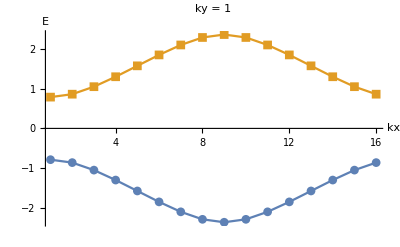

```mathematica
yidxs = Range[1,ny];
Table[
ListPlot[ {lowband[[All,yidx]], highband[[All,yidx]]}, PlotLabel-> "ky = " <> ToString@yidx, AxesLabel->{"kx","E"} ]
,{yidx, yidxs}]
```

#### Viewing the Chern number as rotation over Bloch Sphere

```mathematica
paulivecs = Chop@Table[ pauliVec[ N@HtlssPerK[[x,y]] ] , {x,nx}, {y,ny} ];
Graphics3D[ {Thick,Red, Line[{ {0,0,0}, {0,0,1} } ], Black, Line[ paulivecs[[All,1]] ] } ]
```

-Graphics3D-

Split-step walk, allowing phase transitions

### Comparing the individual walks

#### 1D case

```mathematica
nx = 16;
ny = 1;

(* First walk params, which are topological (C=1) *)
th1 = -Pi/2;
th2 = Pi/4;

(* Second walk params, which are trivial (C=0) *)
phi1 = th1;
phi2 = 3 Pi/4;

makeWalkOperators[nx,ny];
SplitStep1D[th1_, th2_ ]:= ctrlX1.KroneckerProduct[ idXY, Ry[th2] ].ctrlX0.KroneckerProduct[ idXY, Ry[th1] ];
step1  = SplitStep1D[ th1, th2 ];
step2  = SplitStep1D[ phi1, phi2];
```

```mathematica
nsteps = 10;
init = Vec[  pos2idx[Floor[nx/2], Floor[ny/2], 0,nx,ny]-1  ,   2  *nx*ny   ];

walk1 = Table[ MatrixPower[ step1, m ] .init, {m, 0 ,nsteps } ];
walk2 = Table[ MatrixPower[ step2, m ] .init, {m, 0 ,nsteps } ];
probs1 = Table[ amps2probs[ w, nx, ny], {w,walk1} ];
probs2 = Table[ amps2probs[ w, nx, ny], {w,walk2} ];
```

```mathematica
Manipulate[ 
{ MatrixPlot[ probs1[[m]] ] , MatrixPlot[ probs2[[m]] ] }
,{m,1,nsteps,1}]
```

#### Plotting energy bands

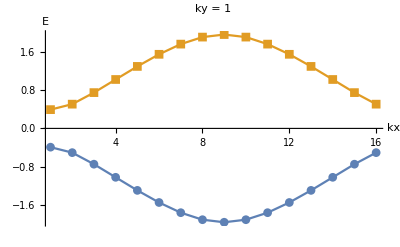
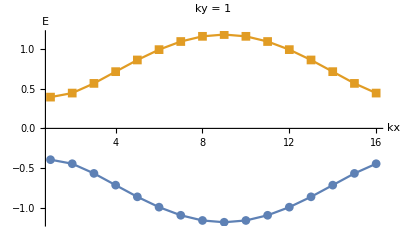

{-Graphics3D-,-Graphics3D-}

```mathematica
{HevalPerK1, paulivecs1} = step2paulivecs[ step1, nx, ny ] ;
{HevalPerK2, paulivecs2} = step2paulivecs[ step2, nx, ny ] ;
{  plotEbands[ HevalPerK1 ] , plotEbands[ HevalPerK2 ]  }
{ plotpaulivecs[ paulivecs1, 1 ], plotpaulivecs[ paulivecs2, 1 ] }
```

#### 2D case

```mathematica
nx = 40;
ny = 40;
makeWalkOperators[nx,ny];

(* Walk 1: select the whole region to be "topological" *)
y0 = 1;
y1 = ny;

(* Inside the region topological (C=1), outside not topological *)
th1In  = 3Pi/2;
th2In =3 Pi/2;
th1Out = 7Pi/6;
th2Out = 7Pi/6;
coinIn = Ry[th1In];
coinOut = Ry[th1Out];

step1 = ctrlX.ctrlY.RegionCoinY[coinIn, coinIn, y0, y1, ny ].ctrlY.RegionCoinY[coinIn, coinIn, y0, y1, ny ] .ctrlX.RegionCoinY[ coinIn, coinIn, y0, y1, ny ]

(* Walk 2: no region is topological *)
step2 = ctrlX.ctrlY.RegionCoinY[coinOut, coinOut, y0, y1, ny ].ctrlY.RegionCoinY[coinOut, coinOut, y0, y1, ny ] .ctrlX.RegionCoinY[ coinOut, coinOut, y0, y1, ny ]
```

SparseArray[<96000>, {3200, 3200}]

SparseArray[<96000>, {3200, 3200}]

```mathematica
{HevalPerK1, pvec1} = step2paulivecs[ step1, nx, ny ] ;
{HevalPerK2, pvec2} = step2paulivecs[ step2, nx, ny ] ;
pvecn1 = Table[ Normalize[ pvec1[[x,y]] ], {x,1,nx}, {y,1,ny} ];
pvecn2 = Table[ Normalize[ pvec2[[x,y]] ], {x,1,nx}, {y,1,ny} ];
```

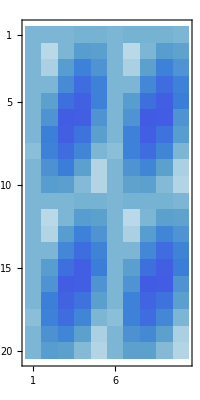
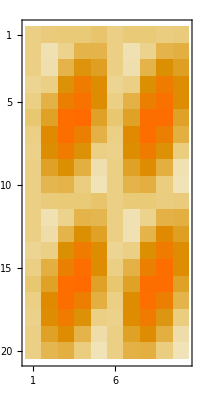

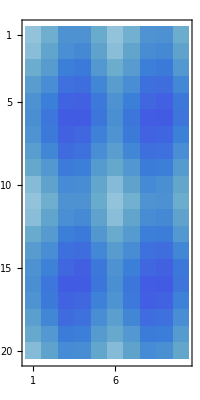
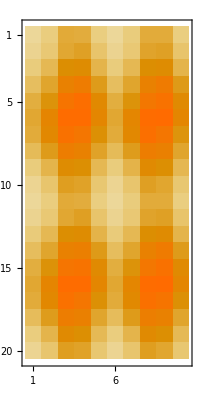

```mathematica
{ MatrixPlot[ HevalPerK1[[All,All,1]] ], MatrixPlot@HevalPerK1[[All,All,2]]  }
{ MatrixPlot[ HevalPerK2[[All,All,1]] ], MatrixPlot@HevalPerK2[[All,All,2]]  }
```

```mathematica
{
Show@Table[ plotpaulivecs[ pvecn1, yidx ], {yidx, 1, ny} ]
,Show@Table[ plotpaulivecsVsX[ pvecn1, xidx ], {xidx, 1, nx} ] 
,Show@Table[ plotpaulivecs[ pvecn2, yidx ], {yidx, 1, ny} ]
,Show@Table[ plotpaulivecsVsX[ pvecn2, xidx ], {xidx, 1, nx} ]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{int1, integrand1} = chernFromPauliVec[ pvecn1 ];
{int2, integrand2} = chernFromPauliVec[ pvecn2 ];
int1
int2
```

-0.613406

-0.000699749

### Creating a phase boundary

#### In 1D

```mathematica
nx = 120;
ny = 1;
makeWalkOperators[nx,ny];

x0 = 1;
x1 = Floor[nx/2];

(* Inside the region topological (C=1), outside not topological *)
th1 = -Pi/2;
th2In = Pi/4;
th2Out = 3Pi/4;
coinIn = Ry[th2In];
coinOut = Ry[th2Out];

step = ctrlX1.RegionCoinX[coinIn, coinOut, x0, x1, nx ] .ctrlX0.KroneckerProduct[ idXY, Ry[th1] ];
```

The initial state with coin flipped to |1> has a much higher chance of standing still.

```mathematica
(* A walker starting on the phase transition area has a large prob to stay: *)
nsteps = 100;
init = Vec[  1,   2  *nx*ny   ];

walk = Table[ MatrixPower[ N@step, m ] .init, {m, 0 ,nsteps } ];
probs = Table[ amps2probs[ w, nx, ny], {w,walk} ];

Manipulate[ 
BarChart[probs[[m,All]]
, PlotRange->{0,1} 
, GridLines->{{x0-1/2, x1+1/2}, {}}
 ]
,{m,1,nsteps,1}]
```

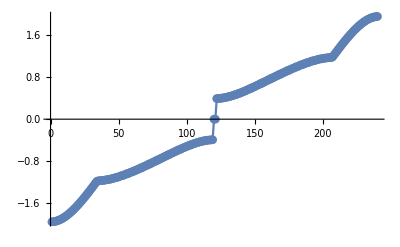

```mathematica
effHam = I MatrixLog[N@ step ] ;
{eval, evec} = Chop@ makeEigenSystem[ effHam ] ;

ListPlot[ Sort@eval ]
```

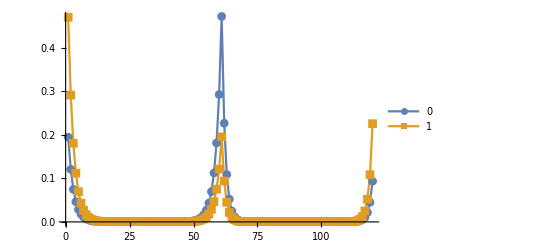

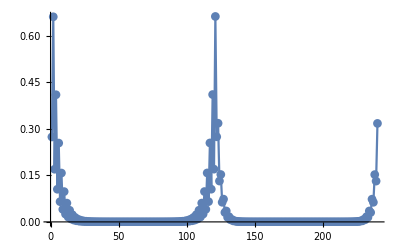

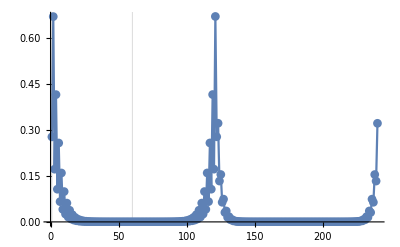

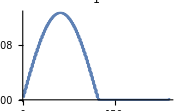
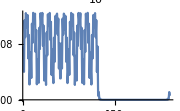
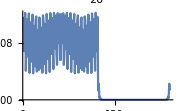
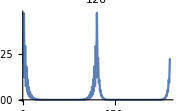
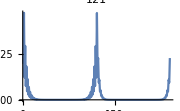

```mathematica
(* Plotting the middle-most states, which are the bound states: *)
(* In the position basis, odd indices correspond to coin 0, evens to coin 1 *)
ListPlot[ { Abs[ evec[[nx, 1;;-1;;2]] ], Abs[ evec[[nx,2;;-1;;2]] ] }, PlotLegends->{"0","1"} ]
ListPlot[ Abs[ evec[[nx]] + evec[[nx+1]] ] ]
ListPlot[ Abs[ evec[[nx]] -evec[[nx+1]]  ], GridLines->{{x0, x1}, {}} ]

(* sample of the other states: *)
vecsToPlot = { 1, 10, 20, nx, nx+1, nx+2, 40, 60 };
Table[  ListPlot[ Abs@evec[[v]]
, PlotLabel->v
, ImageSize->Small
, PlotMarkers->None
 ], {v,vecsToPlot} ]
```

Comparison with Fourier states:

```mathematica
qftX = KroneckerProduct[ qft[nx/2], idY, Id2];
```

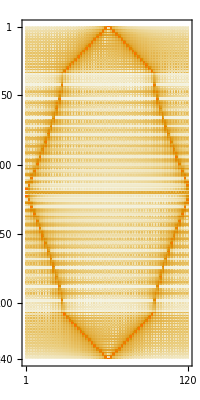

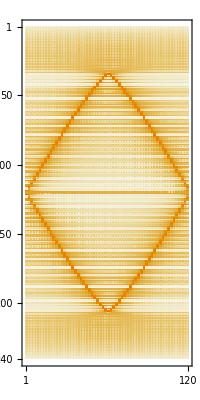

```mathematica
(* Fourier components on the first half: *)
Abs[ evec[[All,1;;nx]] .qftX ] // MatrixPlot

(* And the second half: *)
Abs[ evec[[All,nx+1;;-1]] .qftX ] // MatrixPlot
```

#### In 2D

```mathematica
nx = 20;
ny = 50;
makeWalkOperators[nx,ny];

y0 = 1;
y1 = Floor[nx/2];

(* Inside the region topological (C=1), outside not topological *)
th1In  = 3Pi/2;
th2In =3 Pi/2;
th1Out = 7Pi/6;
th2Out = 7Pi/6;
coinIn = Ry[th1In];
coinOut = Ry[th1Out];

step = ctrlX.ctrlY.RegionCoinY[coinIn, coinOut, y0, y1, ny ].ctrlY.RegionCoinY[coinIn, coinOut, y0, y1, ny ] .ctrlX.RegionCoinY[ coinIn, coinOut, y0, y1, ny ]
```

SparseArray[<60000>, {2000, 2000}]

The initial state with coin flipped to |1> has a much higher chance of standing still.

```mathematica
(* A walker starting on the phase transition area has a large prob to stay: *)
nsteps = 30;
init = Vec[  1,   2  *nx*ny   ];

walk = Table[ MatrixPower[ N@step, m ] .init, {m, 0 ,nsteps } ];
probs = Table[ amps2probs[ w, nx, ny], {w,walk} ];

Manipulate[ 
MatrixPlot[probs[[m]]
, PlotRange->{0,1} 
, GridLines->{{x0-1/2, x1+1/2}, {}}
 ]
,{m,1,nsteps,1}]
```

Part::partd: Part specification probs⟦1⟧ is longer than depth of object.

MatrixPlot::mat0: Argument probs⟦1⟧ at position 1 is not a matrix.

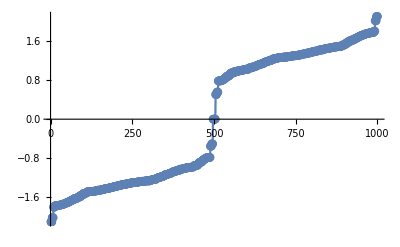

```mathematica
effHam = I MatrixLog[N@ step ] ;
{eval, evec} = Chop@ makeEigenSystem[ effHam ] ;

ListPlot[ Sort@eval ]
```

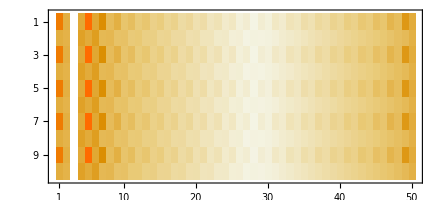

```mathematica
amps2probs[ Sqrt[evec[[nx*ny ]]], nx, ny  ] // MatrixPlot
```

Solving systems using invariance under kx:

```mathematica
qftx = KroneckerProduct[ qft[nx], idY, Id2 ];
stepdiagX = Chop[ qftx†.N[step].qftx ];
blocks = Table[ stepdiagX[[ j;;j+(ny*2)-1, j;;j+(ny*2)-1 ]], {j,1,nx*ny*2, ny*2} ];
Hblocks = Table[ I MatrixLog[ block ], {block, blocks} ];
HevalPerK = Table[ Sort@Chop@Eigenvalues[ Hblock ],{Hblock, Hblocks} ];
```

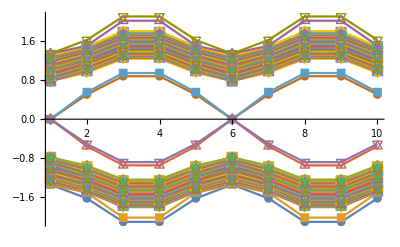

```mathematica
ListPlot[HevalPerKᵀ]
```

# Integration over k:

```mathematica
G  = MatrixExp[ -I (Z+Y)/Sqrt[2] Pi/2 ];
yplus = G.Vec[0,2];
yminus = G.Vec[1,2];
```

#### Just testing the flatten method:

```mathematica
bigN = 4;
nsteps = 3;
gatelist = Table[ {A[k],B[k]}, {k,1,bigN}, {m,1,nsteps}];
MatrixForm /@ ArrayReshape[ gatelist, { bigN*nsteps*2 , 1 } ]
```

{(A[1]),(B[1]),(A[1]),(B[1]),(A[1]),(B[1]),(A[2]),(B[2]),(A[2]),(B[2]),(A[2]),(B[2]),(A[3]),(B[3]),(A[3]),(B[3]),(A[3]),(B[3]),(A[4]),(B[4]),(A[4]),(B[4]),(A[4]),(B[4])}

#### Performing the whole circuit:

Two step integration: (the operator Rz[2 Pi j / N] is equivalent to the “step” operator acting on a state with momentum j).

```mathematica
bigN = 2;
 Ry[t].Rz[2 Pi 1 / bigN].Ry[t].Rz[2 Pi 0 / N] // FullSimplify // MatrixForm
```

(1 | 0
0 | -1)

```mathematica
bigN = 3;
Ry[t].Rz[2 Pi 2 / bigN ] . Ry[t].Rz[2 Pi 1 / bigN].Ry[t].Rz[2 Pi 0 / N] // FullSimplify // MatrixForm
```

(Cos[t/2]^3 | -1/2 (2+ⅈ √3+Cos[t]) Sin[t/2]
1/2 (2-ⅈ √3+Cos[t]) Sin[t/2] | Cos[t/2]^3)

We can plug any EVEN number in, and retrieve the Z operator. (TODO: What does this mean? Is this the dynamic/berry phase for coin states |0> and |1>?)

```mathematica
tmp = Table[ N@{Normal@Ry[t], Rz[2 Pi j / bigN]}, {j,kinit,kinit + 1 bigN +1 },{m,1,nsteps} ]
```

{{{{{0.866025,-0.5},{0.5,0.866025}},{{1.,0.},{0.,1.}}}},{{{{0.866025,-0.5},{0.5,0.866025}},{{1.,0.},{0.,0.+1. ⅈ}}}},{{{{0.866025,-0.5},{0.5,0.866025}},{{1.,0.},{0.,-1.}}}},{{{{0.866025,-0.5},{0.5,0.866025}},{{1.,0.},{0.,0.-1. ⅈ}}}},{{{{0.866025,-0.5},{0.5,0.866025}},{{1.,0.},{0.,1.}}}},{{{{0.866025,-0.5},{0.5,0.866025}},{{1.,0.},{0.,0.+1. ⅈ}}}}}

```mathematica
Range[10][[1;;-3]]
```

{1,2,3,4,5,6,7,8}

24

```mathematica
bigN=20;
nsteps = 1;
kinit = 0;  (* We start with k=0 such that the states |u/d> are the trivial eigenstate *)
t = .4124;
(* The gatelist is ordered like a circuit, and should be reversed before matrix-multiplication *)
(* Note that reversing Ry and Rz operations is equivalent to shifting kinit by one *)
gatelist = Table[ N@{Normal@Ry[t], Rz[2 Pi j / bigN]}, {j,kinit,kinit + 1 bigN},{m,1,nsteps} ];  (* Note: j runs over bigN + 1 steps, returning to the same value as initially *)
gatelist = ArrayReshape[gatelist, {Times@@ Dimensions[gatelist][[1;;-3]],2,2}] ;
res = FullSimplify[ Dot@@(Reverse@gatelist)  ];

MatrixForm /@ (Reverse@gatelist) ; (* All operations as a list *)
res // Chop // MatrixForm  (* Result in comp basis *)
G†.res.G // Chop // MatrixForm  (* Result on the |u/d> states *)
```

(0.978816 | -0.204742
-0.204742 | -0.978816)

(0 | 0.204742-0.978816 ⅈ
0.204742+0.978816 ⅈ | 0)

Tracking the adiabaticity.

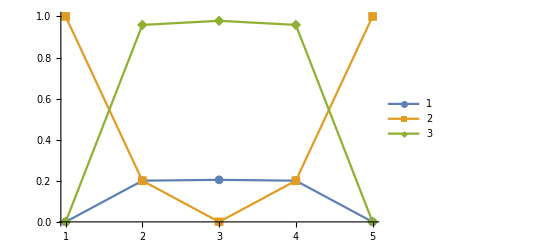

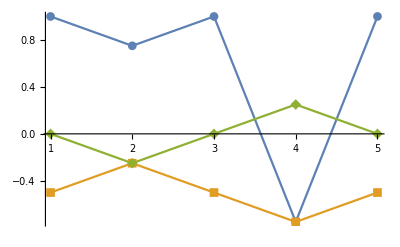

```mathematica
psinit = yplus;
sigma = {X,Y,Z};
opss = Table[ ( Dot@@   ( Reverse@(gatelist[[j;;j+1]]) ) ) , {j,1,Length[gatelist],2} ];
vecss = Table[ (Dot@@ (Reverse@gatelist[[1;;j]])) . psinit , {j,2,Length[gatelist],2} ];
pvecss = Normalize/@( pauliVec/@ opss );
ListPlot[  Evaluate[ Abs[ pvecssᵀ ] ] , PlotLegends->Automatic]
ListPlot[  Evaluate[ Arg[ pvecssᵀ ]/Pi ] ]
```

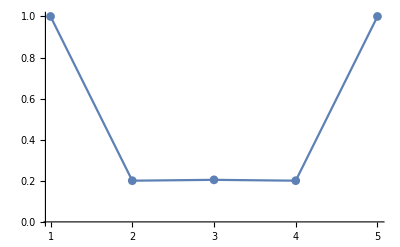

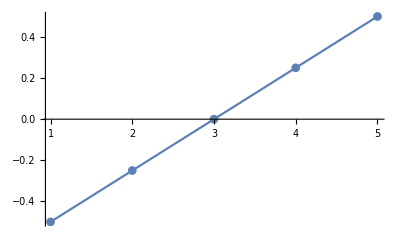

```mathematica
fullness = Table[ vecss[[j]]*.(pvecss[[j]].sigma).vecss[[j]], {j,1,Length[vecss]} ];
ListPlot[ Evaluate@Abs@fullness ]
ListPlot[ Evaluate@Arg@fullness /Pi]
```

Simplifying the operation by commuting the Z operations through Y operations.

- All Z operations at the front add up to (Z)^1.
- The Y operations are transformed into rotations around ϕ = Cos[ϕ] Y - Sin[ϕ] X, where ϕ is the sum over the number of Z-angles commuted through.

For some magical reason, the ϕ-rotations together precisely form the Identity operator!

```mathematica
bigN = 6;
t=.231 + 1;
ints = Table[ j, {j,0,bigN-1} ]
sums = Table[ Total[ ints[[1;;j]] ], {j,1,Length[ints]}]
```

{0,1,2,3,4,5}

{0,1,3,6,10,15}

```mathematica
glist = Table[ N@R[t, s * 2 Pi / bigN] , {s,sums} ];
totres = Dot@@(Reverse@glist) ;
MatrixForm @Chop@ totres
MatrixForm@Chop[G†.totres.G ]
```

(1. | 0
0 | 1.)

(1. | 0
0 | 1.)

#### Split step walk (Kitagawa)

Definition of split-step walk (not possible analytically)

```mathematica
bigN=10;
kinit = 1;
gatelist = Table[ {Normal@Ry[t1], Rz[ 2 Pi k / bigN ], Normal@Ry[t2], Rz[2 Pi k / bigN ] }, {k, kinit, kinit + bigN -1 } ];
gatelist = Flatten[gatelist, 1 ] ;
res = FullSimplify[ Dot@@(Reverse@N@gatelist)  ];
MatrixForm /@ (Reverse@gatelist)
res // MatrixForm
```

$Aborted

{(1 | 0
0 | 1),(Cos[t2/2] | -Sin[t2/2]
Sin[t2/2] | Cos[t2/2]),(1 | 0
0 | 1),(Cos[t1/2] | -Sin[t1/2]
Sin[t1/2] | Cos[t1/2]),(1 | 0
0 | ⅇ^(-(ⅈ π)/5)),(Cos[t2/2] | -Sin[t2/2]
Sin[t2/2] | Cos[t2/2]),(1 | 0
0 | ⅇ^(-(ⅈ π)/5)),(Cos[t1/2] | -Sin[t1/2]
Sin[t1/2] | Cos[t1/2]),(1 | 0
0 | ⅇ^(-(2 ⅈ π)/5)),(Cos[t2/2] | -Sin[t2/2]
Sin[t2/2] | Cos[t2/2]),(1 | 0
0 | ⅇ^(-(2 ⅈ π)/5)),(Cos[t1/2] | -Sin[t1/2]
Sin[t1/2] | Cos[t1/2]),(1 | 0
0 | ⅇ^(-(3 ⅈ π)/5)),(Cos[t2/2] | -Sin[t2/2]
Sin[t2/2] | Cos[t2/2]),(1 | 0
0 | ⅇ^(-(3 ⅈ π)/5)),(Cos[t1/2] | -Sin[t1/2]
Sin[t1/2] | Cos[t1/2]),(1 | 0
0 | ⅇ^(-(4 ⅈ π)/5)),(Cos[t2/2] | -Sin[t2/2]
Sin[t2/2] | Cos[t2/2]),(1 | 0
0 | ⅇ^(-(4 ⅈ π)/5)),(Cos[t1/2] | -Sin[t1/2]
Sin[t1/2] | Cos[t1/2]),(1 | 0
0 | -1),(Cos[t2/2] | -Sin[t2/2]
Sin[t2/2] | Cos[t2/2]),(1 | 0
0 | -1),(Cos[t1/2] | -Sin[t1/2]
Sin[t1/2] | Cos[t1/2]),(1 | 0
0 | ⅇ^((4 ⅈ π)/5)),(Cos[t2/2] | -Sin[t2/2]
Sin[t2/2] | Cos[t2/2]),(1 | 0
0 | ⅇ^((4 ⅈ π)/5)),(Cos[t1/2] | -Sin[t1/2]
Sin[t1/2] | Cos[t1/2]),(1 | 0
0 | ⅇ^((3 ⅈ π)/5)),(Cos[t2/2] | -Sin[t2/2]
Sin[t2/2] | Cos[t2/2]),(1 | 0
0 | ⅇ^((3 ⅈ π)/5)),(Cos[t1/2] | -Sin[t1/2]
Sin[t1/2] | Cos[t1/2]),(1 | 0
0 | ⅇ^((2 ⅈ π)/5)),(Cos[t2/2] | -Sin[t2/2]
Sin[t2/2] | Cos[t2/2]),(1 | 0
0 | ⅇ^((2 ⅈ π)/5)),(Cos[t1/2] | -Sin[t1/2]
Sin[t1/2] | Cos[t1/2]),(1 | 0
0 | ⅇ^((ⅈ π)/5)),(Cos[t2/2] | -Sin[t2/2]
Sin[t2/2] | Cos[t2/2]),(1 | 0
0 | ⅇ^((ⅈ π)/5)),(Cos[t1/2] | -Sin[t1/2]
Sin[t1/2] | Cos[t1/2])}

(Cos[t1] | -Sin[t1]
Sin[t1] | Cos[t1])

```mathematica
ContourPlot[ Abs@Tr[Dot@@(Reverse@gatelist)]/2 , {t1, 0, 2Pi}, {t2, 0, 2Pi}  ]
```

-Graphics-

```mathematica
ContourPlot[ Norm@pauliVec@(Dot@@(Reverse@gatelist)), {t1, 0, 2Pi}, {t2, 0, 2Pi} , PlotLegends->Automatic ]
```

-Graphics-

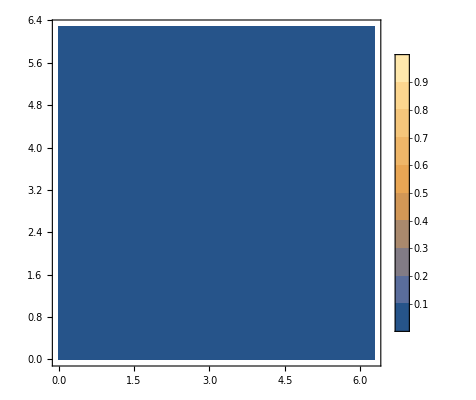
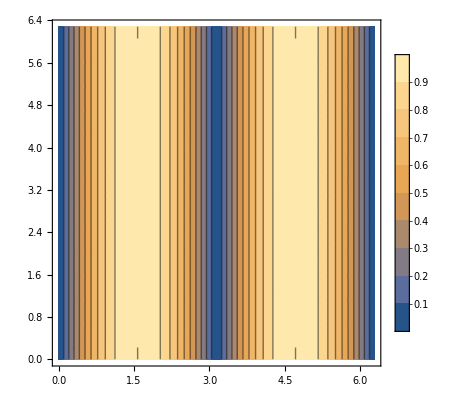
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
pvecabss = Abs@pauliVec[res];
Table[
ContourPlot[ pvecabs/2, {t1,0,2Pi}, {t2, 0, 2Pi} 
, PlotLegends->Automatic
, PlotRange->{0,1}
, ColorFunctionScaling -> False
]

,{pvecabs, pvecabss}]
```

```mathematica
ContourPlot[ Norm[pvecabss/2], {t1,0,2Pi}, {t2, 0, 2Pi}  
, PlotLegends->Automatic]
```

-Graphics-

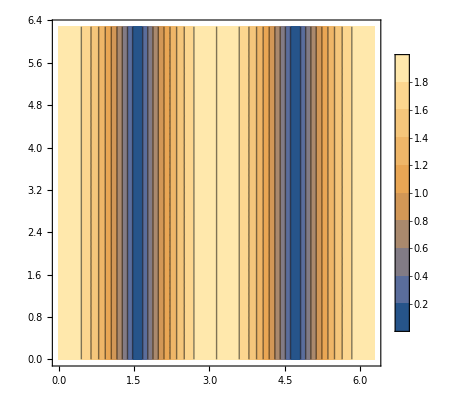

```mathematica
ContourPlot[ Evaluate[Abs@Tr[res]], {t1,0,2Pi}, {t2, 0, 2Pi}  
, PlotLegends->Automatic]
```

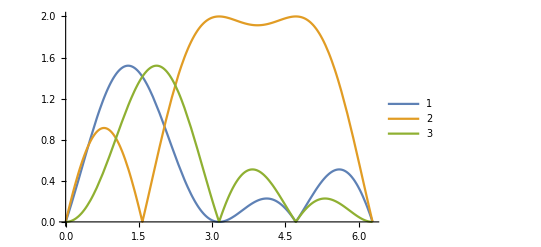

```mathematica
Plot[ Evaluate[Abs@pauliVec[res] /. t1-> Pi/4] , {t2, 0 ,2Pi } ]
```

## Split step walk - broken up into tiny steps

```mathematica
pauliVec[ ham_ ]:= (1/2) * { Tr[X.ham], Tr[Y.ham], Tr[Z.ham] };
pauliNormalize[ pvec_ ]:= If[ Norm[pvec] > 0.001, Normalize[pvec], pvec ];
energyFromPaulis[ pvec_ ]:= Norm[ pvec ];



extraPhase[k_, bigN_] := Exp[ -I 2 Pi k / bigN ];

splitStepBlochOscillatingCoin[ t1_, t2_, bigN_, kinit_:0 ]:= Module[{gatelist, steplist},
	(* The gatelist is ordered like a circuit, and should be reversed before matrix-multiplication *)
	(* Note that reversing Ry and Rz operations is equivalent to shifting kinit by one *)
	gatelist = Table[ N@{ extraPhase[j,bigN] * Normal@Ry[t1], Rz[2 Pi j / bigN],  Normal@Ry[t2], Rz[ 2 Pi j / bigN ]   }, {j,kinit,kinit + 1 bigN} ];  
	(* Note: j runs over bigN + 1 steps, returning to the same value as initially *)
	steplist = Table[ Dot@@Reverse@gatelist[[j]], {j,Length[gatelist]}];
	
	Return[steplist];
];

multiplySteps[ steplist_ ] := Dot@@Reverse@steplist;
multiplyState[ steplist_, initstate_ ]:= Table[ (Dot@@steplist[[1;;j]]).initstate , {j,1,Length[steplist]}];
step2ham[ step_ ]:= I MatrixLog[ step ];
AdiabaticCorrectness[ normveclist_, statelist_ ]:= Module[{miniham},
	Return@Table[ 
		miniham = normveclist[[j]].{X,Y,Z}; 
		Conjugate[statelist[[j]]].miniham.statelist[[j]]
		,{j,1,Length@normveclist}]
];


PlotPauliVecs[ pvecs_, plotrange_:{{-1,1},{-1,1},{-1,1}} ]:= Module[{},
	Graphics3D[ { 
		Line[{{0,0,0},{0,0,1}}]
		, Thick, Line[Chop@pvecs] 
	}, PlotRange->plotrange ]
];

(* Here's a trick to turn a phase into a number between (0,1) *)
sillyPhaseInterference[ cnumber_ ] :=  (1/Pi)*Abs@Arg@cnumber

(* Perform a Bloch Oscillating Quantum Walk. Check the visibility of the obtained phase. *)
topologicalExperiment[ t1_, t2_, bigN_ ]:=Module[{steplist,res, hamlist,pvecs,energies, Etot,resmat},
	steplist = splitStepBlochOscillatingCoin[ t1, t2, bigN ];
	res = multiplySteps[ steplist ] ;
	
	hamlist = step2ham /@ steplist ;
	pvecs = pauliVec /@ hamlist;
	energies = energyFromPaulis /@ pvecs;
	
	(* For Etot, check if we're in the upper or lower band *)
	Etot = Total@energies * Sign[ Chop@pvecs[[1,2]] ];

	resmat = MatrixExp[ I Etot Z].(G†.res.G);
	
	(* Here's a trick to turn a phase into a number between (0,1) *)
	Return[ sillyPhaseInterference[ resmat[[1,1]] ] ];
];
```

#### Example usage:

Raw results:

(0.913941-0.378572 ⅈ | 0.133413+0.05996 ⅈ
-0.133413+0.05996 ⅈ | 0.913941+0.378572 ⅈ)

(0.913941+0.133413 ⅈ | -0.378572-0.05996 ⅈ
0.378572-0.05996 ⅈ | 0.913941-0.133413 ⅈ)

Total global energy added: 1.24985×10^-15

Plots of energies and paulivecs:

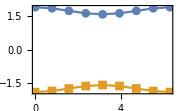
-Graphics--Graphics3D-

Total phase without energies:

(-0.914959-0.126247 ⅈ | 0.379031+0.0569915 ⅈ
-0.379031+0.0569915 ⅈ | -0.914959+0.126247 ⅈ)

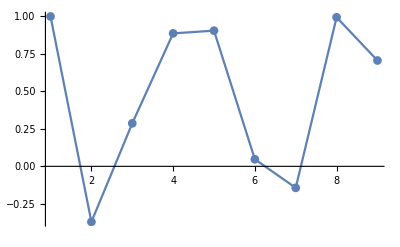
Adiabatic correctness:-Graphics-

```mathematica
bigN=8;
kinit = 0;  (* We start with k=0 such that the states |u/d> are the trivial eigenstate *)
t1 = 1.1Pi ;
t2 = + .1Pi;

(* Generate list of operations *)
steplist = splitStepBlochOscillatingCoin[ t1, t2, bigN, kinit ];

(* Standard multiplication: *)
res = multiplySteps[ steplist ] ;
Print["Raw results: "]
Chop[res,10^-3]  // MatrixForm  (* Result in comp basis *)
Chop[G†.res.G, 10^-3] // MatrixForm  (* Result on the |u/d> states *)

(* Turn operations into Pauli vectors *)
hamlist = step2ham /@ steplist ;
(* Sanity check: there are no constant terms in the Hamiltonian, leading to stray phases *)
Print["Total global energy added: ", Norm@Table[ Tr[ham], {ham,hamlist}] ];
pvecs = pauliVec /@ hamlist;
normvecs = pauliNormalize /@ pvecs;
energies = energyFromPaulis /@ pvecs;
Etot = Total[energies];

Print["Plots of energies and paulivecs:"]
SpectrumAndBlochRotation = Row[{
ListPlot[{energies,-energies}
,Frame-> True
,FrameLabel->{"k","E(k)"}
, ImageSize->Small
, DataRange->{0,2Pi}
], PlotPauliVecs[normvecs]}, "   "]


Print["Total phase without energies:"]
MatrixForm[ Chop[ MatrixExp[ I Etot Z].(G†.res.G ) ] ]

(* Adiabatic errors? *)
initstate = yplus;
states = multiplyState[ steplist, initstate ];
correctness = AdiabaticCorrectness[ normvecs, states ];
Print["Adiabatic correctness:", ListPlot[Re@correctness]];
```

#### Checking visibility for small number of sites

Versus bigN

```mathematica
kinit = 0;  (* We start with k=0 such that the states |u/d> are the trivial eigenstate *)
t1 = .2 Pi;

bigNs = Range[2,30];
t2s = Range[ 0, 2Pi, 2Pi/10 ];

vis = Table[ {t1,t2, bigN,topologicalExperiment[ t1, t2, bigN ]}, {t2, t2s},{bigN, bigNs}];
visflat = Flatten[vis,1];
```

```mathematica
visflat[[1]]
```

{0.628319,0,2,0.2}

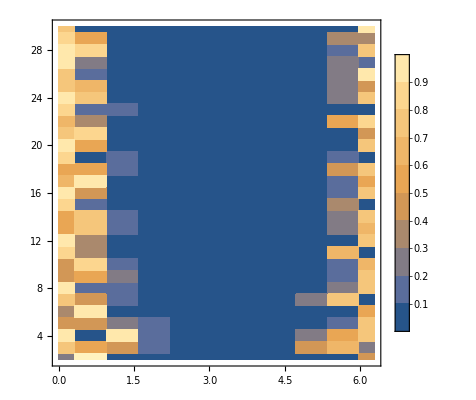

```mathematica
ListContourPlot[visflat[[All,{2,3,4}]], PlotLegends->Automatic, InterpolationOrder->0]
```

Phase diagram

```mathematica
kinit = 0;  (* We start with k=0 such that the states |u/d> are the trivial eigenstate *)
t1 = .2 Pi;

bigN = 8;
t1s = Range[-2Pi,2Pi, 2Pi/10];
t2s = Range[ -2Pi, 2Pi, 2Pi/10 ];

vis = Table[ {t1,t2, bigN,topologicalExperiment[ t1, t2, bigN ]}, {t2, t2s},{t1, t1s}];
visflat = Flatten[vis,1];
```

We do the same for a large N

```mathematica
hugeN = 100;
visLargeN = Table[ {t1,t2, hugeN,topologicalExperiment[ t1, t2, hugeN ]}, {t2, t2s},{t1, t1s}];
visLargeNflat = Flatten[visLargeN,1];
```

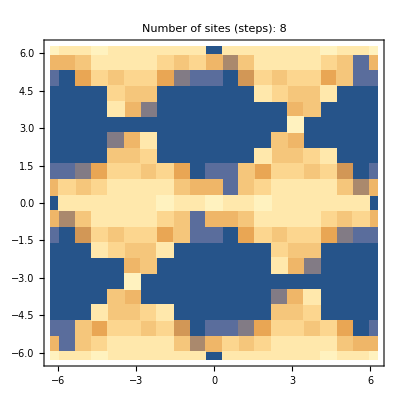

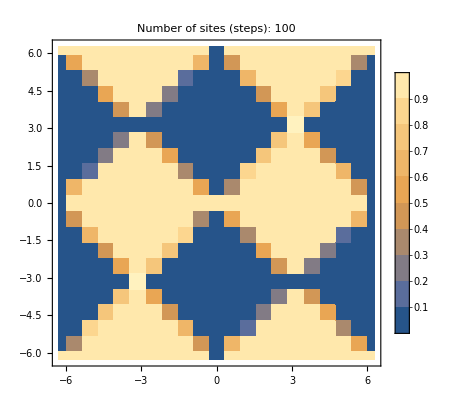

```mathematica
topoPhasesSmallN = ListContourPlot[visflat[[All,{1,2,4}]], PlotLegends->False, InterpolationOrder->0, PlotLabel->"Number of sites (steps): "<>ToString@bigN ]

topoPhasesHugeN = ListContourPlot[visLargeNflat[[All,{1,2,4}]], PlotLegends->Automatic, InterpolationOrder->0, PlotLabel->"Number of sites (steps): "<>ToString@hugeN ]
```

#### Option: Exporting

```mathematica
Export[ "QWSpectrumAndBloch.pdf", SpectrumAndBlochRotation]
```

QWSpectrumAndBloch.pdf

```mathematica
Export[ "QWTopoPhases.pdf",Grid[ {{topoPhasesSmallN, topoPhasesHugeN} }] ]
```

QWTopoPhases.pdf

```mathematica
SpectrumAndBlochRotation
```

-Graphics--Graphics3D-